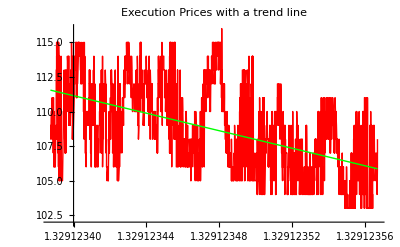

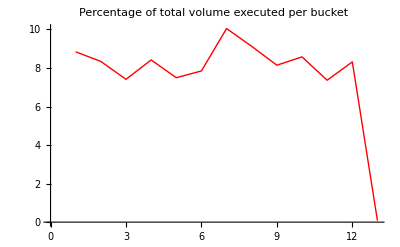

Testing for normal distribution of executed prices

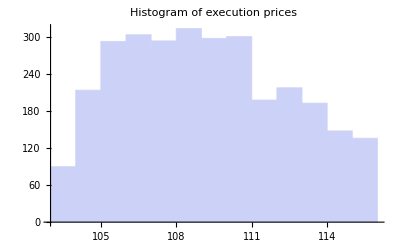

| Statistic | P-Value
Shapiro-Wilk | 0.961691 | 1.74737×10^-27

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Shapiro-Wilk test.

| Statistic | P-Value
Anderson-Darling | 31.0844 | 0.

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Anderson-Darling test.

Testing for normal distribution of submitted prices

-Graphics-

| Statistic | P-Value
Shapiro-Wilk | 0.961691 | 1.74737×10^-27

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Shapiro-Wilk test.

| Statistic | P-Value
Anderson-Darling | 31.0844 | 0.

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Anderson-Darling test.

Testing for normal distribution of new order prices

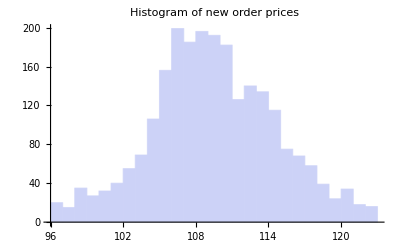

| Statistic | P-Value
Shapiro-Wilk | 0.991908 | 3.42031×10^-10

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Shapiro-Wilk test.

| Statistic | P-Value
Anderson-Darling | 6.31528 | 8.80839×10^-8

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Anderson-Darling test.

```mathematica
ClearAll[report];

report[path_String, filter_Integer, buckets_Integer]:=Module[{executionTimestamp, executionPrice, executionVolume, executionsData, start, stop,executions,executionPricesTimestamps, executionPrices,executionVolumesTimestamps, executionVolumes,executionVolumesBucketed, executionAverageVolumesByBucket,executionPricesLine, newOrderTimestamp, newOrderPrice, newOrderVolume, newOrdersData,newOrders,newOrdersPrices},

executionTimestamp = #[[1]]&;
executionPrice = #[[7]]&;
executionVolume = #[[6]]&;

executionsData = Import[path<> "executions.log"];
start = Min[executionTimestamp[#]&/@executionsData] +  filter * 60 * 1000;
stop = Max[executionTimestamp[#]&/@executionsData];
executions = Sort[Select[executionsData, executionTimestamp[#] > start&], OrderedQ[{executionTimestamp[#],executionTimestamp[#2]}]&];
executionPricesTimestamps ={ executionTimestamp[#], executionPrice[#]}&/@executions;
executionPrices = executionPrice[#]&/@executions;
executionVolumesTimestamps={ executionTimestamp[#], executionVolume[#]}&/@executions;
executionVolumes = executionVolume[#]&/@executions;

executionPricesLine = Fit[executionPricesTimestamps, {1,x}, x];
Print[Show[ListLinePlot[executionPricesTimestamps, PlotStyle->Red], Plot[executionPricesLine, {x, start, stop}, PlotStyle->Green], PlotLabel->"Execution Prices with a trend line"]];

executionVolumesBucketed =Gather[executionVolumesTimestamps, Quotient[executionTimestamp[#]-start,(stop-start)/buckets]==Quotient[executionTimestamp[#2]-start,(stop-start)/buckets]&] ;
executionAverageVolumesByBucket = Total[Map[#[[2]]&,#]]/Total[executionVolumes]*100&/@executionVolumesBucketed;
Print[Show[ListLinePlot[executionAverageVolumesByBucket , PlotStyle->Red], PlotLabel->"Percentage of total volume executed per bucket"]];

Print["Testing for normal distribution of executed prices"];
Print[Show[Histogram[executionPrices], PlotLabel->"Histogram of execution prices"]];
Print[ShapiroWilkTest[executionPrices,"HypothesisTestData"]["TestDataTable"]];
Print[ShapiroWilkTest[executionPrices,"HypothesisTestData"]["TestConclusion"]];
Print[AndersonDarlingTest[executionPrices,Automatic,"HypothesisTestData"]["TestDataTable"]];
Print[AndersonDarlingTest[executionPrices,Automatic,"HypothesisTestData"]["TestConclusion"]];

Print["Testing for normal distribution of submitted prices"];
Print[Show[Histogram[executionPrices], PlotLabel->"Histogram of execution prices"]];
Print[ShapiroWilkTest[executionPrices,"HypothesisTestData"]["TestDataTable"]];
Print[ShapiroWilkTest[executionPrices,"HypothesisTestData"]["TestConclusion"]];
Print[AndersonDarlingTest[executionPrices,Automatic,"HypothesisTestData"]["TestDataTable"]];
Print[AndersonDarlingTest[executionPrices,Automatic,"HypothesisTestData"]["TestConclusion"]];

newOrderTimestamp = #[[1]]&;
newOrderPrice = #[[8]]&;
newOrderVolume = #[[7]]&;
newOrdersData = Import[path<> "newOrders.log"];
newOrders = Sort[Select[newOrdersData, executionTimestamp[#] > start && newOrderPrice[#]>0.&], OrderedQ[{newOrderTimestamp[#],newOrderTimestamp[#2]}]&];
newOrdersPrices = newOrderPrice[#]&/@newOrders;

Print["Testing for normal distribution of new order prices"];
Print[Show[Histogram[newOrdersPrices], PlotLabel->"Histogram of new order prices"]];
Print[ShapiroWilkTest[newOrdersPrices,"HypothesisTestData"]["TestDataTable"]];
Print[ShapiroWilkTest[newOrdersPrices,"HypothesisTestData"]["TestConclusion"]];
Print[AndersonDarlingTest[newOrdersPrices,Automatic,"HypothesisTestData"]["TestDataTable"]];
Print[AndersonDarlingTest[newOrdersPrices,Automatic,"HypothesisTestData"]["TestConclusion"]];
];

report["/Users/jakubkozlowski/Programming/intellij/eugene/demo/eugene/noise/target/noise-0.6-SNAPSHOT/bin/runner/", 2, 12]
```